```mathematica
(*Problem 235*)
R=Sum[(900-3k)r^(k-1),{k,n}];
Eq=(R/.{n->5000})
```

-(3 (-299+300 r-4701 r^5000+4700 r^5001))/(-1+r)^2

```mathematica
Eq2=Expand[Eq*(r-1)^2+600000000000*(r-1)^2]
```

600000000897-1200000000900 r+600000000000 r^2+14103 r^5000-14100 r^5001

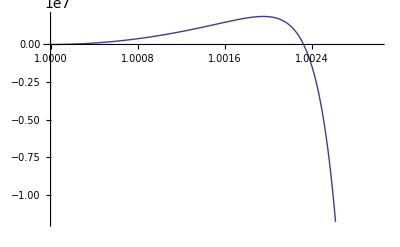

```mathematica
Plot[Eq2,{r,1,1.003}]
```

```mathematica
r/.FindRoot[Eq==-600000000000,{r,1.02},WorkingPrecision->20]
```

1.0023221086328761429